# Piece of Cake grid function test

## Initial data function

```mathematica
ClearAll[omega,nx,ny,nz,nt,w];
omega[wavenumber_]:=Sqrt[Sum[wavenumber[i]^2,{i,1,3}]];
nx[wavenumber_,spaceoffset_,x_]:=wavenumber[1]*(x-spaceoffset[1]);
ny[wavenumber_,spaceoffset_,y_]:=wavenumber[2]*(y-spaceoffset[2]);
nz[wavenumber_,spaceoffset_,z_]:=wavenumber[3]*(z-spaceoffset[3]);
nt[wavenumber_,timeoffset_,t_]:=omega[wavenumber]*(t-timeoffset);
w[wavenumber_,spaceoffset_,timeoffset_,t_,x_,y_,z_]:=2π(nx[wavenumber,spaceoffset,x]+ny[wavenumber,spaceoffset,y]+nz[wavenumber,spaceoffset,z]+nt[wavenumber,timeoffset,t]);

ClearAll[planeWave];
planeWave[wavenumber_,spaceoffset_,timeoffset_,t_,x_,y_,z_]=FullSimplify[Cos[w[wavenumber,spaceoffset,timeoffset,t,x,y,z]]];
```

## Local2global

```mathematica
ClearAll[F];
F[a_,b_,c_]=(((r1-r[c])+(r[c]-r0)Ee[a,b])/(r1-r0))^(1/2);

ClearAll[r];
r[c_]=1/2(r0(1-c)+r1(1+c));

ClearAll[Ee];
Ee[a_,b_]=1+a^2+b^2;

ClearAll[core];
core[a_,b_,c_]=FullSimplify[r[c]/F[a,b,c]];
```

```mathematica
ClearAll[CakePlusX];
CakePlusX={core[a,b,c],b*core[a,b,c],a*core[a,b,c]};

ClearAll[CakePlusY];
CakePlusY={-b*core[a,b,c],core[a,b,c],a*core[a,b,c]};

ClearAll[CakePlusZ];
CakePlusZ={-a*core[a,b,c],b*core[a,b,c],core[a,b,c]};

ClearAll[CakeMinusX];
CakeMinusX={-core[a,b,c],-b*core[a,b,c],a*core[a,b,c]};

ClearAll[CakeMinusY];
CakeMinusY={b*core[a,b,c],-core[a,b,c],a*core[a,b,c]};

ClearAll[CakeMinusZ];
CakeMinusZ={a*core[a,b,c],b*core[a,b,c],-core[a,b,c]};
```

```mathematica
ClearAll[local2global];
local2global[patch_,aa_,bb_,cc_]:=FullSimplify[patch//.{a->aa,b->bb,c->cc}]
```

## Data loading

```mathematica
ClearAll[rootDir,dataDir];
rootDir="/home/lucas/EinsteinToolkit/CactusX/exe";
dataDir="run_cake_coord_self_tests";

ClearAll[parameterFile];
parameterFile=Import[FileNameJoin[{rootDir,dataDir,dataDir<>".par"}],"Text"];

ClearAll[r0,r1];
r0=ToExpression[Flatten[StringCases[parameterFile,RegularExpression["MultiPatch::cake_inner_boundary_radius\\s+=\\s+(\\d+\\.\\d+)"]->{"$1"}]]⟦1⟧];
r1=ToExpression[Flatten[StringCases[parameterFile,RegularExpression["MultiPatch::cake_outer_boundary_radius\\s+=\\s+(\\d+\\.\\d+)"]->{"$1"}]]⟦1⟧];

ClearAll[wavenumber,spaceoffset,timeoffset];
timeoffset=ToExpression[Flatten[StringCases[parameterFile,RegularExpression["TestMultiPatch::time_offset\\s+=\\s+(\\d+\\.\\d+)"]->{"$1"}]]⟦1⟧];

wavenumber[1]=ToExpression[Flatten[StringCases[parameterFile,RegularExpression["TestMultiPatch::wave_number\\[0\\]\\s+=\\s+(\\d+\\.\\d+)"]->{"$1"}]]⟦1⟧];
wavenumber[2]=ToExpression[Flatten[StringCases[parameterFile,RegularExpression["TestMultiPatch::wave_number\\[1\\]\\s+=\\s+(\\d+\\.\\d+)"]->{"$1"}]]⟦1⟧];
wavenumber[3]=ToExpression[Flatten[StringCases[parameterFile,RegularExpression["TestMultiPatch::wave_number\\[2\\]\\s+=\\s+(\\d+\\.\\d+)"]->{"$1"}]]⟦1⟧];

spaceoffset[1]=ToExpression[Flatten[StringCases[parameterFile,RegularExpression["TestMultiPatch::space_offset\\[0\\]\\s+=\\s+(\\d+\\.\\d+)"]->{"$1"}]]⟦1⟧];
spaceoffset[2]=ToExpression[Flatten[StringCases[parameterFile,RegularExpression["TestMultiPatch::space_offset\\[1\\]\\s+=\\s+(\\d+\\.\\d+)"]->{"$1"}]]⟦1⟧];
spaceoffset[3]=ToExpression[Flatten[StringCases[parameterFile,RegularExpression["TestMultiPatch::space_offset\\[2\\]\\s+=\\s+(\\d+\\.\\d+)"]->{"$1"}]]⟦1⟧];

ClearAll[functionName];
functionName="testmultipatch-multipatch_test_gfs.it000000.p0000.tsv";

ClearAll[gfData];
gfData=SemanticImport[FileNameJoin[{rootDir,dataDir,functionName}]];

ClearAll[indexToPatch,indexToInversePatch];
indexToPatch={CakePlusX,CakeMinusX,CakePlusY,CakeMinusY,CakePlusZ,CakeMinusZ};
indexToInversePatch={InverseCakePlusX,InverseCakeMinusX,InverseCakePlusY,InverseCakeMinusY,InverseCakePlusZ,InverseCakeMinusZ};
```

## Plots

### Plot Z slice function

```mathematica
ClearAll[plotZslice];
plotZslice[a_]:=Module[
{data,plusx,minusx,plusy,minusy,central},

data=gfData[Select[(#⟦3⟧==1&&#⟦9⟧==a)&],{10,11,12}];
data=data[All,{(local2global[CakePlusX,a,#⟦1⟧,#⟦2⟧]⟦1⟧)&,(local2global[CakePlusX,a,#⟦1⟧,#⟦2⟧]⟦2⟧)&,3}];
plusx=ListDensityPlot[data,PlotLegends->True];

data=gfData[Select[(#⟦3⟧==2&&#⟦9⟧==a)&],{10,11,12}];
data=data[All,{(local2global[CakeMinusX,a,#⟦1⟧,#⟦2⟧]⟦1⟧)&,(local2global[CakeMinusX,a,#⟦1⟧,#⟦2⟧]⟦2⟧)&,3}];
minusx=ListDensityPlot[data,PlotLegends->True];

data=gfData[Select[(#⟦3⟧==3&&#⟦9⟧==a)&],{10,11,12}];
data=data[All,{(local2global[CakePlusY,a,#⟦1⟧,#⟦2⟧]⟦1⟧)&,(local2global[CakePlusY,a,#⟦1⟧,#⟦2⟧]⟦2⟧)&,3}];
plusy=ListDensityPlot[data,PlotLegends->True];

data=gfData[Select[(#⟦3⟧==4&&#⟦9⟧==a)&],{10,11,12}];
data=data[All,{(local2global[CakeMinusY,a,#⟦1⟧,#⟦2⟧]⟦1⟧)&,(local2global[CakeMinusY,a,#⟦1⟧,#⟦2⟧]⟦2⟧)&,3}];
minusy=ListDensityPlot[data,PlotLegends->True];

Show[
plusx,
minusx,
plusy,
minusy,

PlotRange->{{-r1-1/2,r1+1/2},{-r1-1/2,r1+1/2}},

AspectRatio->1
]
];
```

### Plot error function

```mathematica
ClearAll[plotErrorPatch];
plotErrorPatch[a_,patchIndex_]:=Module[
{filteredGfData},

filteredGfData=gfData[Select[(#⟦3⟧==patchIndex&&#⟦9⟧==a)&],{9,10,11,12}];
filteredGfData=filteredGfData[All,{
(local2global[indexToPatch⟦patchIndex⟧,a,#⟦2⟧,#⟦3⟧]⟦1⟧)&,
(local2global[indexToPatch⟦patchIndex⟧,a,#⟦2⟧,#⟦3⟧]⟦2⟧)&,
(local2global[indexToPatch⟦patchIndex⟧,a,#⟦2⟧,#⟦3⟧]⟦3⟧)&,
4
}
];
filteredGfData=filteredGfData[All,{1,2,Abs[planeWave[wavenumber,spaceoffset,timeoffset,0,#⟦1⟧,#⟦2⟧,#⟦3⟧]-#⟦4⟧]&}];

ListDensityPlot[filteredGfData,PlotLegends->Automatic]
]

ClearAll[plotError];
plotError[a_]:=
Show[
plotErrorPatch[a,1],
plotErrorPatch[a,2],
plotErrorPatch[a,3],
plotErrorPatch[a,4],

PlotRange->{{-r1-1/2,r1+1/2},{-r1-1/2,r1+1/2}},

AspectRatio->1
]
```

### Plot GF

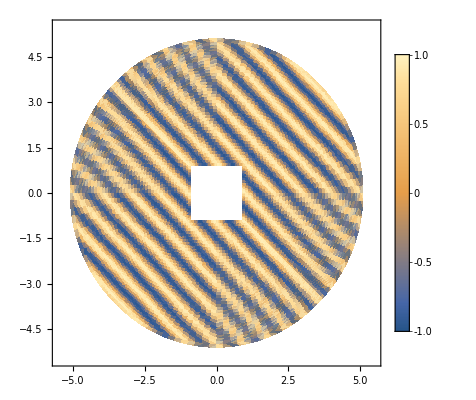

```mathematica
plotZslice[0]
```

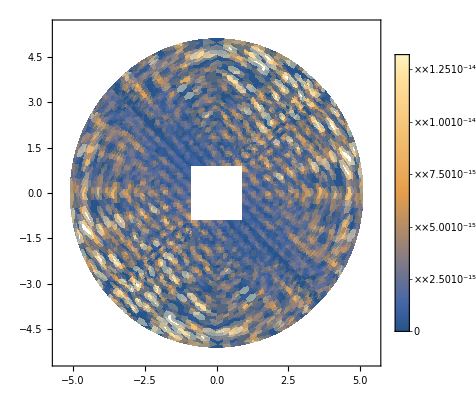

```mathematica
plotError[0]
```